# Figure 5

```mathematica
Hd[q_,p_,t_]=(q^2+p^2)/2-(1/2)*((1+ξ*Cos[(2π)*t/τ])^2+2*g^2*q^2)^(1/2);
```

## Normal phase

```mathematica
g=1/2^(1/2); (*coupling*)
ξ=1/20;(*modulation amplitude*)
```

#### τ≠n/m T(E_0)

```mathematica
τ=10;
tintt=τ;
tf=50000;
```

```mathematica
(*Trajectory 1*)
pin=0.005;
qin=0.005;
solt=NDSolve[{D[q[t],t]==D[Hd[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hd[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt1a=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

```mathematica
(*Trajectory 2*)
pin=0.0;
qin=0.2;
solt=NDSolve[{D[q[t],t]==D[Hd[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hd[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt2a=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

```mathematica
(*Trajectory 3*)
pin=0.0;
qin=0.4;
solt=NDSolve[{D[q[t],t]==D[Hd[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hd[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt3a=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

```mathematica
(*Trajectory 4*)
pin=0.0;
qin=0.6;
solt=NDSolve[{D[q[t],t]==D[Hd[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hd[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt4a=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

```mathematica
(*Trajectory 5*)
pin=0.0;
qin=0.8;
solt=NDSolve[{D[q[t],t]==D[Hd[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hd[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt5a=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

```mathematica
(*Trajectory 6*)
pin=0.0;
qin=1.0;
solt=NDSolve[{D[q[t],t]==D[Hd[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hd[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt6a=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

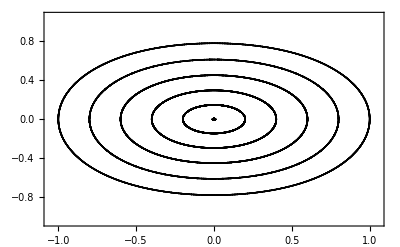

```mathematica
fig=ListPlot[{qprt1a,qprt2a,qprt3a,qprt4a,qprt5a,qprt6a},PlotStyle->{Black},Axes->False,Frame->True,PlotRange->{{-1.05,1.05},{-1.05,1.05}},LabelStyle->{16,Black}]
```

#### τ=T(E_0)

```mathematica
τ=8.768;
tintt=τ;
tf=50000;
```

```mathematica
(*Trajectory 1*)
pin=0.005;
qin=0.005;
solt=NDSolve[{D[q[t],t]==D[Hd[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hd[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt1b=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

```mathematica
(*Trajectory 2*)
pin=0.14;
qin=0.0;
solt=NDSolve[{D[q[t],t]==D[Hd[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hd[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt2b=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

```mathematica
(*Trajectory 3*)
pin=0.0;
qin=0.23;
solt=NDSolve[{D[q[t],t]==D[Hd[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hd[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt3b=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

```mathematica
(*Trajectory 4*)
pin=0.0;
qin=0.3;
solt=NDSolve[{D[q[t],t]==D[Hd[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hd[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt4b=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

```mathematica
(*Trajectory 5*)
pin=0.0;
qin=-0.23;
solt=NDSolve[{D[q[t],t]==D[Hd[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hd[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt5b=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

```mathematica
(*Trajectory 6*)
pin=0.0;
qin=-0.3;
solt=NDSolve[{D[q[t],t]==D[Hd[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hd[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt6b=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

```mathematica
(*Trajectory 7*)
pin=0.0;
qin=0.4;
solt=NDSolve[{D[q[t],t]==D[Hd[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hd[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt7b=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

```mathematica
(*Trajectory 8*)
pin=0.0;
qin=0.6;
solt=NDSolve[{D[q[t],t]==D[Hd[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hd[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt8b=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

```mathematica
(*Trajectory 9*)
pin=0.0;
qin=0.8;
solt=NDSolve[{D[q[t],t]==D[Hd[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hd[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt9b=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

```mathematica
(*Trajectory 10*)
pin=0.0;
qin=1.0;
solt=NDSolve[{D[q[t],t]==D[Hd[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hd[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt10b=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

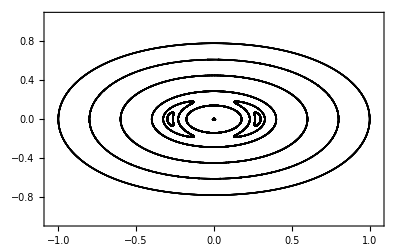

```mathematica
fig=ListPlot[{qprt1b,qprt2b,qprt3b,qprt4b,qprt5b,qprt6b,qprt7b,qprt8b,qprt9b,qprt10b},PlotStyle->{Black},Axes->False,Frame->True,PlotRange->{{-1.05,1.05},{-1.05,1.05}},LabelStyle->{16,Black}]
```

#### τ=1/2 T(E_0)

```mathematica
τ=4.4;
tintt=τ;
tf=50000;
```

```mathematica
(*Trajectory 1*)
pin=0.01;
qin=0.0;
solt=NDSolve[{D[q[t],t]==D[Hd[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hd[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt1c=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

```mathematica
(*Trajectory 2*)
pin=0.25;
qin=0.0;
solt=NDSolve[{D[q[t],t]==D[Hd[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hd[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt2c=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

```mathematica
(*Trajectory 3*)
pin=0.18;
qin=0.0;
solt=NDSolve[{D[q[t],t]==D[Hd[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hd[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt3c=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

```mathematica
(*Trajectory 4*)
pin=0.4;
qin=0.0;
solt=NDSolve[{D[q[t],t]==D[Hd[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hd[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt4c=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

```mathematica
(*Trajectory 5*)
pin=0.0;
qin=0.6;
solt=NDSolve[{D[q[t],t]==D[Hd[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hd[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt5c=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

```mathematica
(*Trajectory 6*)
pin=0.0;
qin=0.8;
solt=NDSolve[{D[q[t],t]==D[Hd[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hd[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt6c=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

```mathematica
(*Trajectory 7*)
pin=0.0;
qin=1.0;
solt=NDSolve[{D[q[t],t]==D[Hd[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hd[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt7c=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

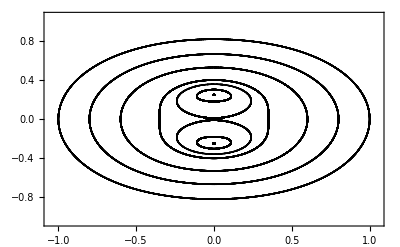

```mathematica
fig=ListPlot[{qprt1c,qprt2c,qprt3c,qprt4c,qprt5c,qprt6c,qprt7c},PlotStyle->{Black},Axes->False,Frame->True,PlotRange->{{-1.05,1.05},{-1.05,1.05}},LabelStyle->{16,Black}]
```

#### τ=1/4 T(E_0)

```mathematica
τ=2.173;
tintt=τ;
tf=50000;
```

```mathematica
(*Trajectory 1*)
pin=0.01;
qin=0.0;
solt=NDSolve[{D[q[t],t]==D[Hd[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hd[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt1d=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

```mathematica
(*Trajectory 2*)
pin=0.0;
qin=0.2;
solt=NDSolve[{D[q[t],t]==D[Hd[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hd[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt2d=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

```mathematica
(*Trajectory 3*)
pin=0.0;
qin=0.27;
solt=NDSolve[{D[q[t],t]==D[Hd[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hd[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt3d=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

```mathematica
(*Trajectory 4*)
pin=0.0;
qin=0.4;
solt=NDSolve[{D[q[t],t]==D[Hd[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hd[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt4d=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

```mathematica
(*Trajectory 5*)
pin=0.0;
qin=0.6;
solt=NDSolve[{D[q[t],t]==D[Hd[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hd[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt5d=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

```mathematica
(*Trajectory 6*)
pin=0.0;
qin=0.8;
solt=NDSolve[{D[q[t],t]==D[Hd[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hd[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt6d=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

```mathematica
(*Trajectory 7*)
pin=0.0;
qin=1.0;
solt=NDSolve[{D[q[t],t]==D[Hd[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hd[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt7d=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

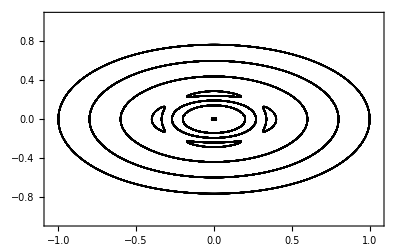

```mathematica
fig=ListPlot[{qprt1d,qprt2d,qprt3d,qprt4d,qprt5d,qprt6d,qprt7d},PlotStyle->{Black},Axes->False,Frame->True,PlotRange->{{-1.05,1.05},{-1.05,1.05}},LabelStyle->{16,Black}]
```

## Superradiant phase

```mathematica
g=2^(1/2); (*coupling*)
ξ=1/20;(*modulation amplitude*)
```

#### τ≠n/m T(E_0)

```mathematica
τ=10;
tintt=τ;
tf=50000;
```

```mathematica
(*Trajectory 1*)
pin=0.01;
qin=0.0;
solt=NDSolve[{D[q[t],t]==D[Hd[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hd[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt1e=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

```mathematica
(*Trajectory 2*)
pin=0.0;
qin=0.4;
solt=NDSolve[{D[q[t],t]==D[Hd[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hd[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt2e=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

```mathematica
(*Trajectory 3*)
pin=0.0;
qin=-0.4;
solt=NDSolve[{D[q[t],t]==D[Hd[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hd[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt3e=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

```mathematica
(*Trajectory 4*)
pin=0.0;
qin=0.61;
solt=NDSolve[{D[q[t],t]==D[Hd[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hd[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt4e=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

```mathematica
(*Trajectory 5*)
pin=0.0;
qin=-0.61;
solt=NDSolve[{D[q[t],t]==D[Hd[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hd[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt5e=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

```mathematica
(*Trajectory 6*)
pin=0.0;
qin=0.8;
solt=NDSolve[{D[q[t],t]==D[Hd[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hd[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt6e=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

```mathematica
(*Trajectory 7*)
pin=0.0;
qin=-0.8;
solt=NDSolve[{D[q[t],t]==D[Hd[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hd[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt7e=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

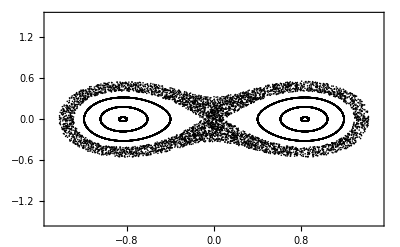

```mathematica
fig=ListPlot[{qprt1e,qprt2e,qprt3e,qprt4e,qprt5e,qprt6e,qprt7e},PlotStyle->{Black},Axes->False,Frame->True,PlotRange->{{-1.5,1.5},{-1.5,1.5}},LabelStyle->{16,Black}]
```

#### τ=T(E_0)

```mathematica
τ=14.7;
tintt=τ;
tf=50000;
```

```mathematica
(*Trajectory 1*)
pin=0.0;
qin=0.01;
solt=NDSolve[{D[q[t],t]==D[Hd[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hd[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt1f=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

```mathematica
(*Trajectory 2*)
pin=0.0;
qin=0.4;
solt=NDSolve[{D[q[t],t]==D[Hd[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hd[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt2f=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

```mathematica
(*Trajectory 3*)
pin=0.0;
qin=-0.4;
solt=NDSolve[{D[q[t],t]==D[Hd[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hd[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt3f=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

```mathematica
(*Trajectory 4*)
pin=0.0;
qin=0.81;
solt=NDSolve[{D[q[t],t]==D[Hd[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hd[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt4f=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

```mathematica
(*Trajectory 5*)
pin=0.0;
qin=0.72;
solt=NDSolve[{D[q[t],t]==D[Hd[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hd[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt5f=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

```mathematica
(*Trajectory 6*)
pin=0.0;
qin=0.98;
solt=NDSolve[{D[q[t],t]==D[Hd[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hd[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt6f=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

```mathematica
(*Trajectory 7*)
pin=0.0;
qin=1.09;
solt=NDSolve[{D[q[t],t]==D[Hd[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hd[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt7f=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

```mathematica
(*Trajectory 8*)
pin=0.0;
qin=-0.81;
solt=NDSolve[{D[q[t],t]==D[Hd[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hd[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt8f=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

```mathematica
(*Trajectory 9*)
pin=0.0;
qin=-0.72;
solt=NDSolve[{D[q[t],t]==D[Hd[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hd[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt9f=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

```mathematica
(*Trajectory 10*)
pin=0.0;
qin=-0.98;
solt=NDSolve[{D[q[t],t]==D[Hd[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hd[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt10f=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

```mathematica
(*Trajectory 11*)
pin=0.0;
qin=-1.09;
solt=NDSolve[{D[q[t],t]==D[Hd[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hd[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt11f=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

```mathematica
(*Trajectory 12*)
pin=0.0;
qin=1.07;
solt=NDSolve[{D[q[t],t]==D[Hd[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hd[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt12f=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

```mathematica
(*Trajectory 13*)
pin=0.0;
qin=-1.07;
solt=NDSolve[{D[q[t],t]==D[Hd[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hd[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt13f=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

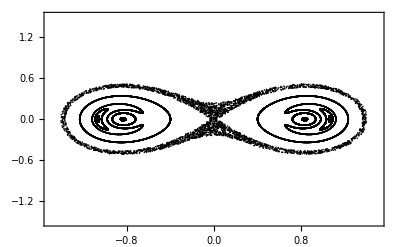

```mathematica
fig=ListPlot[{qprt1f,qprt2f,qprt3f,qprt4f,qprt5f,qprt6f,qprt7f,qprt8f,qprt9f,qprt10f,qprt11f,qprt12f,qprt13f},PlotStyle->{Black},Axes->False,Frame->True,PlotRange->{{-1.5,1.5},{-1.5,1.5}},LabelStyle->{16,Black}]
```

```mathematica
Export["trajectories_resonant_n1m1_int.png",fig]
```

trajectories_resonant_n1m1_int.png

#### τ=1/2 T(E_0)

```mathematica
τ=7.35;
tintt=τ;
tf=50000;
```

```mathematica
(*Trajectory 1*)
pin=0.01;
qin=0.0;
solt=NDSolve[{D[q[t],t]==D[Hd[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hd[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt1g=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

```mathematica
(*Trajectory 2*)
pin=0.0;
qin=0.8;
solt=NDSolve[{D[q[t],t]==D[Hd[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hd[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt2g=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

```mathematica
(*Trajectory 3*)
pin=0.0;
qin=-0.8;
solt=NDSolve[{D[q[t],t]==D[Hd[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hd[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt3g=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

```mathematica
(*Trajectory 4*)
pin=0.0;
qin=1.22;
solt=NDSolve[{D[q[t],t]==D[Hd[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hd[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt4g=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

```mathematica
(*Trajectory 5*)
pin=0.0;
qin=-1.22;
solt=NDSolve[{D[q[t],t]==D[Hd[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hd[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt5g=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

```mathematica
(*Trajectory 6*)
pin=0.0;
qin=1.05;
solt=NDSolve[{D[q[t],t]==D[Hd[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hd[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt6g=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

```mathematica
(*Trajectory 7*)
pin=0.0;
qin=-1.05;
solt=NDSolve[{D[q[t],t]==D[Hd[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hd[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt7g=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

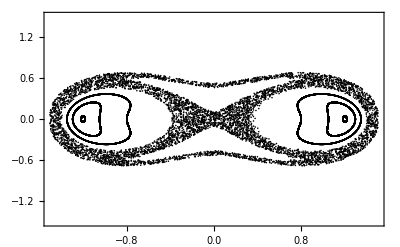

```mathematica
fig=ListPlot[{qprt1g,qprt2g,qprt3g,qprt4g,qprt5g,qprt6g,qprt7g},PlotStyle->{Black},Axes->False,Frame->True,PlotRange->{{-1.5,1.5},{-1.5,1.5}},LabelStyle->{16,Black}]
```

```mathematica
Export["trajectories_resonance_n1m2_int.png",fig]
```

trajectories_resonance_n1m2_int.png

#### τ=1/4 T(E_0)

```mathematica
τ=3.704;
tintt=τ;
tf=50000;
```

```mathematica
(*Trajectory 1*)
pin=0.01;
qin=0.0;
solt=NDSolve[{D[q[t],t]==D[Hd[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hd[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt1h=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

```mathematica
(*Trajectory 2*)
pin=0.0;
qin=0.4;
solt=NDSolve[{D[q[t],t]==D[Hd[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hd[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt2h=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

```mathematica
(*Trajectory 3*)
pin=0.0;
qin=0.6;
solt=NDSolve[{D[q[t],t]==D[Hd[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hd[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt3h=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

```mathematica
(*Trajectory 4*)
pin=0.0;
qin=0.7;
solt=NDSolve[{D[q[t],t]==D[Hd[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hd[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt4h=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

```mathematica
(*Trajectory 5*)
pin=0.0;
qin=0.85;
solt=NDSolve[{D[q[t],t]==D[Hd[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hd[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt5h=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

```mathematica
(*Trajectory 6*)
pin=0.18;
qin=0.85;
solt=NDSolve[{D[q[t],t]==D[Hd[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hd[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt6h=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

```mathematica
(*Trajectory 7*)
pin=0.25;
qin=0.85;
solt=NDSolve[{D[q[t],t]==D[Hd[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hd[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt7h=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

```mathematica
(*Trajectory 8*)
pin=0.0;
qin=-0.4;
solt=NDSolve[{D[q[t],t]==D[Hd[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hd[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt8h=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

```mathematica
(*Trajectory 9*)
pin=0.0;
qin=-0.6;
solt=NDSolve[{D[q[t],t]==D[Hd[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hd[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt9h=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

```mathematica
(*Trajectory 10*)
pin=0.0;
qin=-0.7;
solt=NDSolve[{D[q[t],t]==D[Hd[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hd[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt10h=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

```mathematica
(*Trajectory 11*)
pin=0.0;
qin=-0.85;
solt=NDSolve[{D[q[t],t]==D[Hd[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hd[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt11h=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

```mathematica
(*Trajectory 12*)
pin=0.18;
qin=-0.85;
solt=NDSolve[{D[q[t],t]==D[Hd[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hd[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt12h=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

```mathematica
(*Trajectory 13*)
pin=0.25;
qin=-0.85;
solt=NDSolve[{D[q[t],t]==D[Hd[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hd[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt13h=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

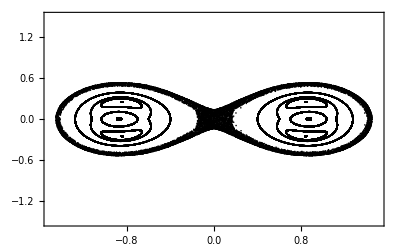

```mathematica
fig=ListPlot[{qprt1h,qprt2h,qprt3h,qprt4h,qprt5h,qprt6h,qprt7h,qprt8h,qprt9h,qprt10h,qprt11h,qprt12h,qprt13h},PlotStyle->{Black},Axes->False,Frame->True,PlotRange->{{-1.5,1.5},{-1.5,1.5}},LabelStyle->{16,Black}]
```